## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TPI";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

(dhap^c⇌g3p^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 0.107411 | 0.102041
0.112782 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 9000 | 8833
9167 | 1/s | 7.6 | 25 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities =Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(dhap^c⇌g3p^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null | 0.107411 | 0.102041
0.112782 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 9000 | 8833
9167 | 1/s | 7.6 | 25 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_TPI[c] + dhap[c] <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c] + g3p[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,((TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c)^TPI2,((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,Overscript[(TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c, TPI2],((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

```mathematica
haldaneRatiosList
```

{(k_TPI1^⟶ k_TPI2^⟶ k_TPI3^⟶)/(k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)}

```mathematica
unifiedRateConstList
```

{}

## Semi-Automated Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["TPISimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["TPISimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.1074113856
1	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
1	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
1	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
1	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
1	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
1	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
1	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
1	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
1	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
1	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
1	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9000

### Simulate data with uncertainty

```mathematica
Export["TPISimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["TPISimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=2;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateFor_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateFor_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/TPI/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFileName, lmaResultsFileName, numTrials, dataPathList]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFileName;
dataFilePath = dataPath;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileName, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
haldaneRatio_1 | 5.8013×10^-7 | 3.36551×10^-13 | 0.00013358 | 0.107971 | 0.107971
relRateRev_g3p | 0.0157475 | 0.000247985 | 3.69254 | 0.0909091 | 0.0942659
relRateRev_g3p | 0.0149386 | 0.000223163 | 3.49959 | 0.136807 | 0.141595
relRateRev_g3p | 0.013814 | 0.000190828 | 3.23193 | 0.20076 | 0.207248
relRateRev_g3p | 0.0123416 | 0.000152315 | 2.88252 | 0.284747 | 0.292955
relRateRev_g3p | 0.010558 | 0.000111471 | 2.46086 | 0.386863 | 0.396383
relRateRev_g3p | 0.0085904 | 0.0000737949 | 1.9977 | 0.5 | 0.509989
relRateRev_g3p | 0.00663169 | 0.0000439793 | 1.53872 | 0.613137 | 0.622571
relRateRev_g3p | 0.00487134 | 0.0000237299 | 1.12798 | 0.715253 | 0.723321
relRateRev_g3p | 0.00342883 | 0.0000117569 | 0.792642 | 0.79924 | 0.805575
relRateRev_g3p | 0.00233362 | 5.44576×10^-6 | 0.538781 | 0.863193 | 0.867844
relRateRev_g3p | 0.0015493 | 2.40034×10^-6 | 0.357378 | 0.909091 | 0.91234
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09
absRateRev | 3.01087×10^-8 | 9.06533×10^-16 | 6.93278×10^-6 | 9156.09 | 9156.09

### Simulated Data and Best Fit Data Plot

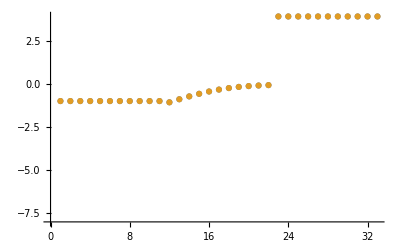

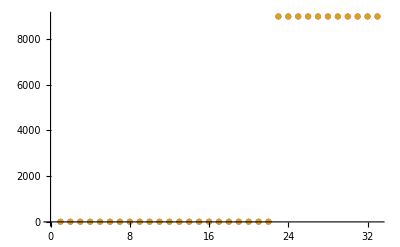

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

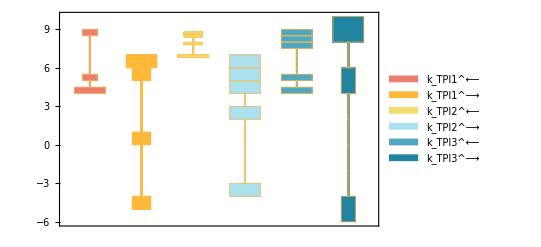

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

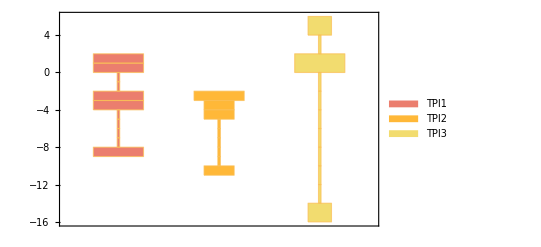

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

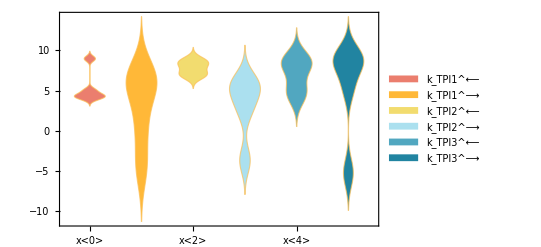

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

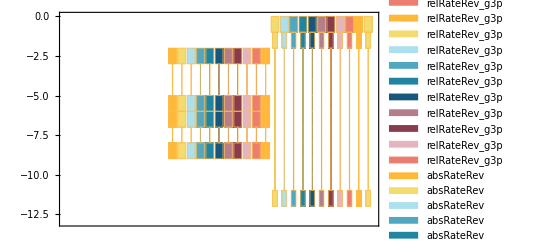

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 5;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00103 | 0.000502615 | 51.2024

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
9000 | 8999.99 | 0.000126519

```mathematica
backCalculateRatios[haldaneDataList[[1]][[1]], haldaneDataList[[1]][[2]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.107411 | 0.107412 | 0.000953614